```mathematica
(* Final *)
```

```mathematica
(* Step 1
Practicing visualization 
*)

(* MIT Sloan Data *)
(* Explain Data *)
path=NotebookDirectory[]
```

C:\Users\User 1\Documents\Final-Project-Kacham\

```mathematica
dataset1 = Import[path<>"NexGen13newPlays.xlsx"]
```

{{{Play Id, X Position, Y Position, Possession Id, Distance, Vertical Distance, Total Distance, Thrower id, Reciever Id, Breakthrow?, Stall Six?, Stall Eight?, Defender Id, Stall?, Block?, Throwaway?, Intercept?, Drop?, Score?, Home Attacking Right?, Point Id, Game Id, Opponent Name, Last X, Last Y, Next X, Next Y, Home on Offense},2808,{442#1371831469#1374520755#9#120,8398.,7141., 442#1371831469#1374520755#9#23,57.889,5.225,58.124,14, 442#1371831469#1374520755, Madison 13,3945.,8186., null, null, true}}}
 |  |  |  |

```mathematica
keys=dataset1[[1,1]]
```

{Play Id, X Position, Y Position, Possession Id, Distance, Vertical Distance, Total Distance, Thrower id, Reciever Id, Breakthrow?, Stall Six?, Stall Eight?, Defender Id, Stall?, Block?, Throwaway?, Intercept?, Drop?, Score?, Home Attacking Right?, Point Id, Game Id, Opponent Name, Last X, Last Y, Next X, Next Y, Home on Offense}

```mathematica
papersummary= Dataset[Map[Association[Thread[Rule[keys,#]]]&,dataset1[[1,2;;Length[dataset1[[1]]]]]]]
```

Dataset[<>]

```mathematica
papersummarychangeddata= papersummary[All,{5->(Quantity[#,"Feet"]&)}][All,{6->(Quantity[#,"Feet"]&)}][All,{7->(Quantity[#,"Feet"]&)}]
```

Dataset[<>]

```mathematica
datasetxy = papersummarychangeddata[All,{2,3}]
```

Dataset[<>]

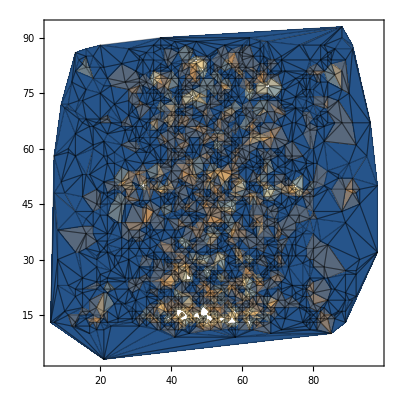

```mathematica
ListDensityPlot[Counts[Round[Normal@Values[datasetxy]/100]],Mesh->All]
```

```mathematica
datasetDistance= papersummarychangeddata[All,{5,6}]
```

Dataset[<>]

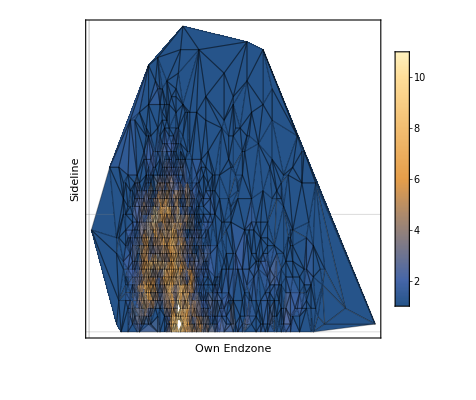

```mathematica
ListDensityPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],Mesh->All,PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"},FrameTicks->{None,None},GridLines->{{-30,-30},{0,15}}]
(* This is showing probability of scoring as a function of field position *)
```

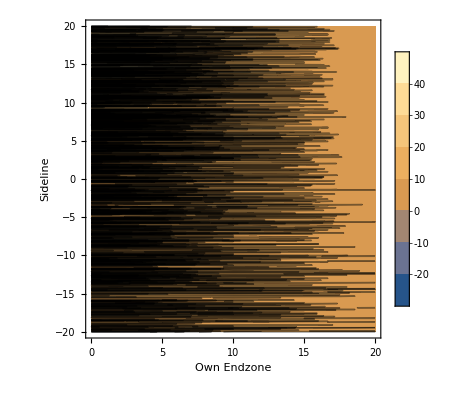

```mathematica
(* Plots that dont actually make sense but look cool *)
(* ask Carlo if it's cat vomit *)
ListContourPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"},DataRange-> {{20,0},{-20,20}}]
```

```mathematica
(* Step 2 *)
(* Adding Ultimate Frisbee Raw Data to the Wolfram Data Repository and representing raw data *)
(* Website: Ultianalytics *)
(* Scrape raw data for all featured AUDL teams 2014 - 2017 *)
```

```mathematica
html=Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\mainpage.txt","Text"]; (* Ultianalytics Home Page *)
```

```mathematica
names={"Chicago Wildfire","Cincinnati Revolution","DC Breeze","Detroit Mechanix","Indianapolis AlleyCats","Madison Radicals","Minnesota Wind Chill","Montreal Royal","New York Empire","Philadelphia Phoenix","Rochester Dragons","Salt Lake Lions","San Francisco FlameThrowers","San Jose Spiders","Seattle Raptors","Toronto Rush","Vancouver Riptide","Atlanta Hustle","Charlotte Express","Chicago Wildfire","Cincinnati Revolution","DC Breeze","Detroit Mechanix","Indianapolis AlleyCats","Jacksonville Cannons","Los Angeles Aviators","Madison Radicals ","Minnesota Wind Chill ","Montreal Royal","Nashville Nightwatch","New York Empire","Ottawa Outlaws ","Philadelphia Phoenix","Pittsburgh Thunderbirds","Raleigh Flyers ","Rochester Dragons","San Diego Growlers","San Francisco FlameThrowers","San Jose Spiders","Seattle Cascades","Toronto Rush ","Vancouver Riptide","Atlanta Hustle","Austin Sol","Charlotte Express","Chicago Wildfire","Cincinnati Revolution","DC Breeze","Dallas Roughnecks","Detroit Mechanix","Indianapolis AlleyCats","Jacksonville Cannons","Los Angeles Aviators","Madison Radicals ","Minnesota Wind Chill ","Montreal Royal","Nashville Nightwatch","New York Empire","Ottawa Outlaws ","Philadelphia Phoenix","Pittsburgh Thunderbirds","Raleigh Flyers ","San Diego Growlers","San Francisco FlameThrowers","San Jose Spiders","Seattle Cascades","Toronto Rush ","Vancouver Riptide","Atlanta Hustle","Austin Sol","Chicago Wildfire","DC Breeze","Dallas Roughnecks","Detroit Mechanix","Indianapolis AlleyCats","Jacksonville Cannons","Los Angeles Aviators","Madison Radicals ","Minnesota Wind Chill ","Montreal Royal","Nashville Nightwatch","New York Empire","Ottawa Outlaws ","Philadelphia Phoenix","Pittsburgh Thunderbirds","Raleigh Flyers ","San Diego Growlers","San Francisco FlameThrowers","San Jose Spiders","Seattle Cascades","Toronto Rush ","Vancouver Riptide"};
```

```mathematica
keys={"Date/Time","Tournamemnt","Opponent","Point Elapsed Seconds","Line","Our Score - End of Point","Their Score - End of Point","Event Type","Action","Passer","Receiver","Defender","Hang Time (secs)","Player 0","Player 1","Player 2","Player 3","Player 4","Player 5","Player 6","Player 7","Player 8","Player 9","Player 10","Player 11","Player 12","Player 13","Player 14","Player 15","Player 16","Player 17","Player 18","Player 19","Player 20","Player 21","Player 22","Player 23","Player 24","Player 25","Player 26","Player 27","Elapsed Time (secs)"};
```

```mathematica
ids={"5762298832486400","5199348879065088","5104011879383040","5634601401712640","5688687119564800","5173627930542080","5646521009700864","5672188833169408","5719707252424704","5701394610782208","5658753101725696","5736577883963392","5672878150254592","5767202099691520","5700228501995520","5666961832804352","5721191432060928","5740216795004928","5712818124881920","5654595548217344","5655358173347840","5753798823772160","5707300165648384","5711261467672576","5664284977659904","5128666635829248","5640136574369792","5691616589250560","5069252692279296","5705148370255872","5206956054675456","5769906008096768","5201331526565888","5723974822526976","4919856549855232","5114556594520064","5142198416834560","5686487861428224","5749730717990912","5632202645700608","5153306812874752","5675918433452032","5758196635402240","5199033182191616","5664810037411840","5743365039587328","5716256766296064","4860723440123904","5764281479987200","6327231433408512","5708939920408576","5643517367943168","5671536392404992","5674069752020992","5635093192245248","5738275486564352","5724822843686912","5633494390669312","5118639615246336","5070544437248000","5683257223938048","5753050442498048","5705718560718848","5704221898833920","5751646390845440","5641462360309760","5651757665353728","5684793748488192","5670377556541440","5734743547052032","5758048710688768","5722152447770624","5681589568667648","5754980359208960","5701751084679168","5471866718257152","5732910535540736","4868028676177920","5684961520648192","5075454121738240","5182111044599808","5638404075159552","5753341694967808","6220853180104704","5663684521099264","5682238511382528","5662069344960512","5094953273262080","6597766625099776","5648334039547904","5131065358286848","6226234774126592"};
```

```mathematica
teams=StringCases[html,"<a href=\"app/#/"~~x:Shortest[__]~~"/players\">"~~y:Shortest[__]~~"</a>":>{x,y}];
```

```mathematica
importTeam[{id_,name_}]:=Module[{data,keys},
data=Import["http://www.ultianalytics.com/rest/view/team/"<>id<>"/stats/export"];
keys=data⟦1⟧;
Dataset[Association[Thread[keys⟦;;Min[Length[#],52]⟧->#⟦;;Min[Length[#],52]⟧]]&/@Drop[data,1]][All,<|"ID"->id,"Name"->name,#|>&]
]
```

```mathematica
i=0;
SetSharedVariable[i];
PrintTemporary[Dynamic[{ProgressIndicator[i/Length[teams]],i}]];
teamDatasets=ParallelMap[(PrintTemporary[++i];importTeam[#])&,teams];
CloseKernels[];
```

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
allData=Join@@teamDatasets
```

Dataset[<>]

```mathematica
DumpSave["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\data\\dataset.mx",allData];
```

```mathematica
Get["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\data\\dataset.mx"];
```

```mathematica
(* Check if all good *)
```

```mathematica
FirstPosition[Normal@allData,_?(Length[#]>50&)]
```

{33663}

```mathematica
allDataUniform=allData[All,If[Length[#]==54,#,Join[#,<|"Absolute Distance"->Missing[],"Begin Area"->Missing[],"Begin X"->Missing[],"Begin Y"->Missing[],"Distance Unit of Measure"->Missing[],"End Area"->Missing[],"End X"->Missing[],"End Y"->Missing[],"Lateral Distance"->Missing[],"Toward Our Goal Distance"->Missing[]|>]]&]
```

Dataset[<>]

```mathematica
curatedData=
allDataUniform[All,{"Date/Time"->DateObject,"Point Elapsed Seconds"->(Quantity[#,"Seconds"]&),"Absolute Distance"->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Lateral Distance" ->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Hang Time (secs)"->(Quantity[#,"Seconds"]&),"Toward Our Goal Distance"->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Elapsed Time (secs)"->(Quantity[#,"Seconds"]&)}];
```

```mathematica
datasetulti= KeyDrop[curatedData,"Distance Unit of Measure"];
```

```mathematica
DumpSave["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\datasetulti.mx",datasetulti];
```

```mathematica
(* Compare some data *)
```

```mathematica
(* Comparing Point Elapsed Seconds 2014 - 2017 teams *)
(* What does that mean: *)
```

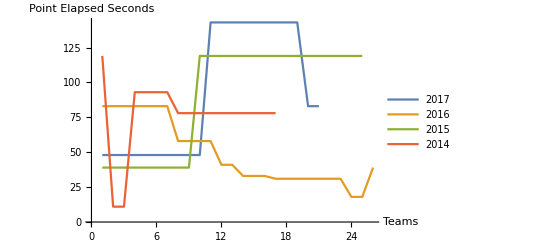

```mathematica
data1 = datasetulti[4 ;;24,6];
data2 = datasetulti[25 ;; 50,6];
data3 = datasetulti[51;; 75,6];
data4 = datasetulti[76;; 92,6];
ListLinePlot[{data1, data2,data3,data4},PlotLegends->{"2017","2016","2015","2014"},AxesLabel->{"Teams","Point Elapsed Seconds"}]
```

```mathematica
(* Filled out the data repository form, got ap ublisher id, waiting for approval *)
```

```mathematica
(* Step 3 *)
(* UltiAnalytics Summary Data AUDL teams 2017 *)
```

```mathematica
(* Goal - Help people understand Ultimate Frisbee tactics and work more with visualization *)
```

```mathematica
path=NotebookDirectory[]
```

C:\Users\User 1\Documents\Final-Project-Kacham\

```mathematica
rawdata=Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\SummaryStatsAllTeams.xlsx","Data"]
```

{{{Year,Team,Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},821,{,,Total,,,,,,,,,,,,,,,,,,89.2728,,,95.5018,,,,}}}
 |  |  |  |

```mathematica
keys=rawdata[[1,1]]
```

{Year,Team,Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls}

```mathematica
teamssummary2017= Dataset[Map[Association[Thread[Rule[keys,#]]]&,rawdata[[1,2;;Length[rawdata[[1]]]]]]]
```

Dataset[<>]

```mathematica
teamssummary2017set2 = teamssummary2017[All,{21->(Quantity[#,"Percent"]&)}][All,{24->(Quantity[#,"Percent"]&)}][All,{27 ->( Quantity[#,"Seconds"]&)}]
```

Dataset[<>]

```mathematica
totalPointsPlayedAllTeams = Total[teamssummary2017[All,If[!NumberQ[#["Points played"]],0,#["Points played"]]&]]
```

93293.5

```mathematica
totalOLine = Total[teamssummary2017[All,If[!NumberQ[#["O-line points played"]],0,#["O-line points played"]]&]]
```

46547.

```mathematica
totalDLine = Total[teamssummary2017[All,If[!NumberQ[#["D-line points played"]],0,#["D-line points played"]]&]]
```

46746.5

```mathematica
(* Comparing players from AUDL 2017 teams *)
```

```mathematica
(* Comparing O-line points played to D-line points played *)
(* Plot 1 *)
```

```mathematica
datasetOline =Normal@ Values[teamssummary2017set2[All,{8,3}]];
```

```mathematica
datasetDline =Normal@ Values[teamssummary2017set2[All,{10,3}]];
```

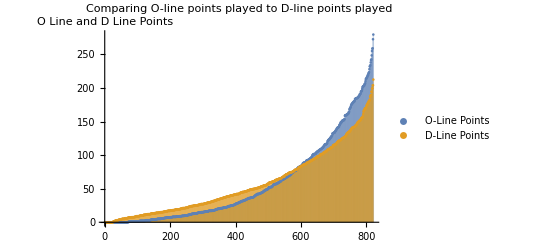

```mathematica
ListPlot[{Tooltip[#[[1]],#[[2]]]&/@SortBy[datasetOline,First],Tooltip[#[[1]],#[[2]]]&/@SortBy[datasetDline,First]},AxesLabel->{None,HoldForm["O Line and D Line Points"]},Ticks->{None,Automatic},PlotLabel->"Comparing O-line points played to D-line points played",PlotLegends->{"O-Line Points","D-Line Points"},Filling->Bottom]
```

```mathematica
datasetPline =Normal@ Values[teamssummary2017set2[All,{8,3,10}]];
```

```mathematica
(* Add Hover for each player *)
```

```mathematica
ListPlot3D[SortBy[datasetPline,Last][[All,{1,3}]]]
```

-Graphics3D-

```mathematica
ListPlot3D[SortBy[datasetPline,First][[All,{1,3}]]]
```

-Graphics3D-

```mathematica
ListPlot3D[MapIndexed[{#1[[1]],#1[[3]],First[#2]}&,SortBy[datasetPline,First]]]
```

-Graphics3D-

```mathematica
ListPlot3D[MapIndexed[{#1[[1]],#1[[3]],First[#2]}&,SortBy[datasetPline,Last]]]
```

-Graphics3D-

```mathematica
datasetPline2=Normal@ Values[teamssummary2017set2[All,{9,8,3,10}]];
```

```mathematica
Map[{#1[[1]],#1[[2]],#[[4]]}&,SortBy[datasetPline2,Last]]
```

```mathematica
data={{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,1.,0.},{1.,10.,0.},{-3.,15.,1.},{0.,0.,1.},{2.,4.,1.},{8.,16.5,1.5},{26.,66.,1.5},{-2.,2.5,2.},{3.,15.,2.},{11.,12.5,2.},{2.,8.5,2.5},{20.,44.,2.5},{28.,36.,2.5},{7.,30.,3.},{13.,28.,3.},{22.,32.,3.},{25.,35.,3.},{27.,36.,3.},{0.,8.,3.5},{28.,56.5,3.5},{36.,69.,3.5},{-2.,17.,4.},{0.,0.,4.},{2.,17.,4.},{9.,25.,4.},{26.,56.,4.},{10.,40.,4.5},{30.,117.5,4.5},{42.,64.,4.5},{0.,0.,5.},{0.,0.,5.},{1.,7.,5.},{7.,20.,5.},{7.,24.,5.},{11.,31.,5.},{43.,101.,5.},{85.,158.5,5.},{3.,5.,5.5},{41.,48.,5.5},{-1.,1.,6.},{-1.,4.,6.},{0.,0.,6.},{6.,67.,6.},{15.,78.,6.},{25.,52.,6.},{39.,92.5,6.},{0.,0.,6.5},{6.,25.5,6.5},{35.,73.5,6.5},{59.,141.5,6.5},{-1.,0.5,7.},{0.,0.,7.},{0.,1.,7.},{1.,21.,7.},{2.,7.,7.},{43.,73.,7.},{49.,111.,7.},{61.,198.5,7.},{0.,0.,7.5},{0.,0.,7.5},{0.,0.,7.5},{0.,0.,7.5},{13.,17.,7.5},{16.,48.,7.5},{30.,42.,7.5},{41.,64.,7.5},{70.,171.,7.5},{-1.,1.,8.},{0.,0.,8.},{1.,1.,8.},{31.,52.5,8.},{59.,115.5,8.},{90.,195.,8.5},{-1.,1.,9.},{0.,36.,9.},{1.,1.,9.},{5.,10.,9.},{5.,16.,9.},{31.,61.,9.},{55.,116.,9.},{68.,121.,9.},{69.,125.5,9.},{-1.,1.,9.5},{6.,37.,9.5},{20.,52.5,9.5},{24.,62.5,9.5},{-1.,1.,10.},{-1.,2.,10.},{0.,0.,10.},{0.,0.,10.},{0.,0.,10.},{1.,7.,10.},{2.,7.5,10.},{24.,67.,10.},{43.,111.,10.},{0.,0.,11.},{0.,1.,11.},{11.,37.,11.},{12.,33.,11.},{15.,39.,11.},{67.,141.5,11.},{87.,153.,11.},{0.,14.5,11.5},{7.,33.,11.5},{48.,164.,11.5},{52.,134.,11.5},{108.,223.5,11.5},{-2.,3.,12.},{-1.,0.5,12.},{-1.,4.5,12.},{1.,17.,12.},{8.,8.,12.},{16.,44.,12.},{43.,133.5,12.},{44.,58.5,12.},{51.,101.5,12.},{-1.,2.,12.5},{0.,0.,12.5},{62.,101.,12.5},{-1.,1.,13.},{0.,0.,13.},{0.,0.,13.},{0.,0.,13.},{0.,0.,13.},{1.,3.,13.},{3.,19.,13.},{34.,97.5,13.},{36.,93.5,13.},{38.,132.5,13.5},{42.,110.,13.5},{78.,123.5,13.5},{108.,221.5,13.5},{114.,234.,13.5},{-1.,1.,14.},{0.,0.,14.},{0.,2.,14.},{1.,1.,14.},{7.,10.5,14.},{20.,37.,14.},{40.,93.,14.},{60.,116.5,14.},{117.,191.,14.},{0.,0.,14.5},{4.,30.,14.5},{8.,65.,14.5},{27.,58.,14.5},{85.,191.,14.5},{0.,0.,15.},{0.,0.,15.},{22.,48.5,15.},{29.,103.5,15.},{57.,136.5,15.},{58.,108.,15.},{58.,129.,15.},{71.,152.,15.},{0.,0.,15.5},{0.,2.,15.5},{3.,15.,15.5},{3.,37.5,15.5},{58.,116.,15.5},{0.,0.,16.},{0.,0.,16.},{0.,1.,16.},{26.,49.,16.},{59.,133.,16.},{0.,0.,16.5},{10.,56.5,16.5},{42.,102.,16.5},{66.,132.,16.5},{-1.,4.,17.},{0.,0.,17.},{1.,3.,17.},{3.,31.,17.},{8.,21.,17.},{15.,43.5,17.},{53.,132.,17.},{99.,196.,17.},{-2.,7.,17.5},{0.,0.,17.5},{18.,57.,17.5},{20.,39.5,17.5},{43.,107.,17.5},{62.,112.,17.5},{103.,187.,17.5},{0.,2.,18.},{0.,4.,18.},{1.,1.5,18.},{2.,2.5,18.},{71.,232.5,18.},{116.,203.,18.},{-1.,1.,18.5},{0.,0.,18.5},{0.,1.,18.5},{21.,63.5,18.5},{-1.,1.,19.},{0.,0.,19.},{5.,7.,19.},{8.,13.,19.},{23.,30.5,19.},{28.,151.5,19.},{38.,60.5,19.},{44.,77.,19.},{65.,116.,19.},{82.,161.,19.},{85.,140.,19.},{151.,255.,19.},{62.,148.5,19.5},{2.,14.,20.},{4.,4.,20.},{7.,16.,20.},{25.,151.5,20.},{59.,123.5,20.},{7.,20.,20.5},{19.,53.,20.5},{-3.,2.,21.},{0.,0.,21.},{0.,0.,21.},{0.,1.,21.},{0.,5.,21.},{10.,22.,21.},{11.,34.5,21.},{19.,66.,21.},{54.,146.5,21.},{0.,1.,21.5},{29.,139.,21.5},{54.,104.,21.5},{59.,151.,21.5},{103.,189.5,21.5},{122.,241.5,21.5},{-4.,13.,22.},{3.,10.,22.},{-1.,12.5,22.5},{6.,24.,22.5},{0.,0.,23.},{14.,43.5,23.},{37.,98.,23.},{77.,178.,23.},{3.,3.,23.5},{61.,94.,23.5},{98.,174.,23.5},{-3.,2.,24.},{-2.,20.,24.},{2.,6.5,24.},{8.,45.,24.},{51.,126.5,24.},{74.,124.5,24.},{-2.,2.5,24.5},{1.,1.5,24.5},{23.,84.5,24.5},{60.,217.5,24.5},{62.,144.5,24.5},{151.,279.5,24.5},{0.,0.,25.},{16.,24.,25.},{23.,134.5,25.},{26.,45.,25.},{29.,106.,25.},{30.,168.,25.},{77.,184.,25.},{82.,214.,25.},{29.,113.,25.5},{65.,140.,25.5},{104.,203.5,25.5},{-4.,7.,26.},{-1.,1.,26.},{20.,41.,26.},{85.,188.,26.},{86.,150.,26.},{11.,20.,26.5},{60.,185.,26.5},{-2.,5.,27.},{0.,0.,27.},{1.,1.,27.},{4.,92.,27.},{8.,17.,27.},{15.,38.,27.},{15.,80.5,27.},{16.,52.,27.},{51.,71.,27.},{0.,0.,27.5},{0.,0.,27.5},{90.,183.5,27.5},{-1.,41.,28.},{0.,3.,28.},{2.,46.5,28.},{7.,13.5,28.},{25.,38.,28.},{74.,146.,28.},{7.,19.,28.5},{-2.,4.,29.},{0.,15.5,29.},{2.,18.,29.},{52.,148.5,29.},{81.,176.,29.},{113.,215.5,29.},{1.,10.,29.5},{21.,69.,29.5},{51.,100.,29.5},{76.,159.5,29.5},{-1.,1.,30.},{105.,222.,30.},{-2.,2.,30.5},{1.,1.,30.5},{8.,13.,30.5},{48.,108.5,30.5},{66.,159.5,31.},{98.,216.,31.},{-3.,2.5,31.5},{-1.,0.5,31.5},{1.,7.,31.5},{84.,184.5,31.5},{0.,0.,32.},{3.,3.,32.},{81.,183.5,32.},{107.,242.5,32.},{87.,177.,32.5},{-4.,7.,33.},{14.,76.5,33.},{58.,122.5,33.},{71.,136.,33.},{0.,8.,33.5},{-2.,9.,34.},{8.,33.,34.},{12.,28.,34.},{45.,71.,34.},{64.,138.,34.},{103.,232.,34.},{3.,7.,34.5},{20.,92.5,34.5},{40.,75.,35.},{48.,203.,35.},{74.,150.,35.},{84.,175.,35.},{86.,161.,35.},{123.,210.,35.},{-1.,17.,35.5},{-3.,5.,36.},{11.,57.,36.},{92.,188.5,36.},{-4.,22.5,36.5},{1.,12.5,36.5},{1.,13.,36.5},{-9.,67.,37.},{-4.,22.,37.},{-2.,7.,37.},{143.,272.5,37.},{18.,122.,37.5},{30.,120.5,37.5},{0.,0.,38.},{16.,30.,38.},{37.,83.,38.},{92.,160.,38.},{-3.,25.,38.5},{-1.,24.,38.5},{27.,65.,38.5},{43.,144.5,38.5},{80.,185.5,38.5},{-1.,17.5,39.},{3.,36.5,39.},{84.,142.,39.},{-2.,6.,39.5},{91.,164.5,39.5},{-4.,5.,40.},{-1.,14.5,40.},{0.,0.,40.},{3.,11.,40.},{100.,219.,40.},{109.,213.,40.},{-3.,16.,40.5},{-2.,3.,40.5},{24.,81.5,40.5},{-6.,9.5,41.},{-1.,2.,41.},{0.,8.,41.},{86.,186.5,41.},{92.,185.,41.},{125.,238.,41.},{14.,35.,41.5},{107.,184.5,41.5},{-1.,1.,42.},{0.,1.,42.},{8.,22.,42.},{18.,60.5,42.},{29.,73.5,42.},{34.,111.,42.},{84.,178.,42.},{89.,170.,42.},{0.,9.,42.5},{31.,54.5,43.},{110.,171.5,43.},{45.,195.,43.5},{-2.,2.,44.},{-1.,4.,44.},{21.,95.5,44.},{62.,106.,44.},{0.,12.5,44.5},{3.,32.,44.5},{-2.,2.,45.},{-1.,5.,45.},{0.,8.,45.},{2.,4.,45.},{30.,83.5,45.},{57.,123.,45.},{0.,4.5,45.5},{31.,95.,45.5},{41.,76.5,45.5},{97.,179.,45.5},{1.,7.,46.},{12.,37.,46.},{36.,74.,46.},{77.,194.5,46.},{37.,84.,46.5},{-1.,1.5,47.},{8.,11.,47.},{-1.,3.5,47.5},{1.,4.5,47.5},{32.,109.,47.5},{37.,179.5,47.5},{-3.,4.,48.},{0.,0.,48.},{0.,4.5,48.5},{2.,10.,48.5},{2.,29.,48.5},{36.,64.5,48.5},{18.,49.,49.},{29.,46.5,49.},{68.,133.,49.},{84.,202.,49.},{93.,214.,49.},{-1.,5.5,49.5},{1.,1.,49.5},{1.,3.,49.5},{7.,15.,49.5},{29.,97.,49.5},{92.,179.5,49.5},{-2.,4.,50.},{3.,9.,50.},{7.,16.5,50.},{-2.,2.,50.5},{-2.,3.5,50.5},{28.,57.,50.5},{113.,180.,50.5},{4.,5.,51.},{4.,9.,51.},{80.,159.,51.},{107.,184.5,51.},{-2.,8.,51.5},{0.,0.,51.5},{68.,259.,51.5},{0.,0.,52.},{4.,17.5,52.},{14.,68.5,52.},{1.,57.,52.5},{-2.,5.,53.},{0.,2.,53.},{5.,63.,53.},{18.,92.,53.},{80.,161.,53.},{13.,26.,53.5},{-1.,5.,54.},{6.,25.5,54.},{117.,205.5,54.},{-4.,8.5,54.5},{74.,152.,54.5},{1.,3.,55.},{3.,13.,55.},{20.,59.5,55.},{75.,153.5,55.},{81.,169.,55.},{4.,12.5,55.5},{9.,11.5,55.5},{141.,258.5,55.5},{3.,31.5,56.},{0.,8.5,57.},{2.,8.,57.},{23.,67.5,57.},{114.,205.5,57.},{1.,13.,58.},{58.,159.5,58.5},{-4.,7.5,59.},{1.,4.,59.},{91.,148.5,59.},{0.,4.5,59.5},{15.,28.5,59.5},{82.,152.,59.5},{111.,191.5,59.5},{-1.,11.5,60.},{31.,83.,60.},{73.,162.,60.},{-2.,2.,60.5},{4.,17.5,60.5},{28.,113.5,60.5},{-7.,21.5,61.},{0.,4.,61.},{51.,219.,61.},{91.,181.,61.5},{31.,128.,62.},{-2.,24.5,62.5},{22.,82.,62.5},{-1.,2.,63.},{2.,11.,63.},{76.,142.,63.},{5.,76.,63.5},{12.,31.5,63.5},{20.,89.,63.5},{11.,47.,64.},{69.,133.5,64.},{-6.,15.5,64.5},{-4.,13.,64.5},{13.,76.5,64.5},{-4.,8.,65.},{4.,57.,65.},{10.,18.,65.},{39.,141.,65.},{-6.,58.5,65.5},{-1.,5.5,65.5},{4.,12.,66.},{14.,92.,66.},{-1.,7.5,67.},{16.,67.,67.},{-1.,13.,67.5},{2.,8.,67.5},{0.,0.,68.},{0.,17.5,68.},{2.,25.,68.},{8.,57.5,68.},{-3.,10.,70.},{11.,50.,70.},{130.,228.,70.},{32.,76.,70.5},{1.,6.,71.},{8.,20.,71.},{9.,23.5,71.5},{35.,88.5,71.5},{41.,95.5,71.5},{-1.,13.,72.},{0.,11.,72.5},{2.,15.,72.5},{96.,176.5,72.5},{10.,19.,73.5},{46.,116.5,73.5},{-4.,10.5,74.},{1.,1.,74.},{68.,248.5,74.},{-2.,6.5,74.5},{-2.,23.,74.5},{-1.,7.,74.5},{4.,9.,74.5},{16.,63.,74.5},{0.,6.5,75.},{1.,6.,75.},{9.,16.,75.5},{96.,202.,75.5},{-2.,59.,76.},{23.,84.,76.},{-1.,3.,77.},{60.,159.5,77.},{-6.,15.5,78.},{0.,17.,78.},{10.,68.5,78.},{11.,52.,78.},{-2.,7.5,78.5},{0.,11.5,78.5},{8.,36.5,78.5},{0.,0.,79.},{6.,26.,79.},{39.,89.5,79.},{1.,5.,80.5},{20.,42.,81.},{-2.,15.,81.5},{1.,8.5,81.5},{8.,25.,82.},{13.,109.5,82.},{16.,88.,82.},{9.,47.,83.},{32.,62.5,83.},{45.,82.5,83.},{-2.,7.5,83.5},{2.,6.5,83.5},{0.,1.5,84.},{24.,51.5,84.},{-6.,17.5,85.},{11.,102.,85.},{1.,8.,85.5},{81.,207.,85.5},{-3.,8.5,86.},{0.,22.,86.},{1.,14.,86.},{11.,28.,86.5},{15.,44.,86.5},{17.,88.5,86.5},{2.,65.,87.},{24.,40.,87.},{-3.,21.,88.},{-3.,9.5,88.5},{9.,20.5,88.5},{36.,104.,88.5},{-1.,6.,89.},{9.,94.5,89.},{6.,108.5,89.5},{18.,109.5,89.5},{52.,105.,90.},{-4.,9.,90.5},{3.,4.5,90.5},{17.,89.,90.5},{41.,162.,91.},{1.,8.5,91.5},{-3.,22.5,92.},{-1.,5.5,92.},{3.,21.,92.},{5.,34.,92.5},{-2.,25.,93.},{3.,21.,93.},{45.,100.,93.5},{-4.,56.5,94.},{2.,24.,94.},{14.,107.,94.},{-3.,6.5,94.5},{0.,3.,94.5},{-2.,8.,95.},{15.,101.5,95.},{19.,60.,95.5},{-3.,2.,96.},{7.,52.5,96.},{25.,89.,97.},{-2.,8.,97.5},{-2.,19.5,97.5},{-2.,9.5,98.},{10.,27.,98.},{32.,60.,98.},{-2.,3.5,98.5},{1.,9.5,98.5},{10.,36.,99.},{12.,91.,99.},{21.,33.5,100.},{11.,54.,100.5},{-6.,9.5,101.},{-4.,8.5,101.},{-3.,15.5,101.},{6.,34.5,101.},{45.,88.,101.5},{11.,52.,102.},{22.,69.5,102.},{53.,128.5,102.},{1.,14.5,102.5},{0.,57.5,103.5},{-8.,12.5,104.},{-3.,23.5,104.},{15.,31.5,104.5},{18.,35.5,104.5},{22.,86.,104.5},{0.,14.5,105.5},{2.,11.5,105.5},{23.,117.5,105.5},{-1.,19.,106.},{2.,6.,106.},{2.,1.5,107.5},{3.,22.,107.5},{10.,35.5,108.},{2.,14.5,108.5},{36.,80.5,108.5},{19.,94.,109.},{30.,82.,109.},{93.,201.,109.},{-3.,5.5,109.5},{10.,29.,109.5},{43.,106.5,110.5},{-4.,20.,111.},{13.,86.5,111.},{1.,11.5,111.5},{25.,75.5,111.5},{3.,10.,112.},{39.,92.5,112.},{13.,37.,113.},{32.,89.5,114.5},{3.,7.5,115.},{8.,27.,115.},{27.,101.5,115.},{30.,72.,115.},{0.,11.,115.5},{97.,186.,115.5},{-4.,14.5,116.},{8.,102.,116.},{9.,84.5,116.5},{-6.,16.,117.},{-2.,9.5,118.},{-2.,17.5,118.},{1.,15.,119.},{-1.,15.,120.},{3.,8.5,120.},{-10.,22.,120.5},{-6.,22.,120.5},{10.,45.5,121.},{-8.,9.5,121.5},{-1.,5.,122.},{0.,69.5,122.},{8.,31.5,122.},{0.,34.5,122.5},{1.,32.5,123.},{10.,81.5,123.5},{1.,5.5,124.},{5.,13.,124.5},{7.,52.5,124.5},{-4.,15.5,125.},{7.,20.,125.5},{50.,136.5,125.5},{1.,20.5,126.},{1.,24.5,126.},{11.,44.5,126.},{1.,29.5,127.},{2.,21.,127.5},{18.,49.,127.5},{7.,26.,128.},{5.,26.,129.},{0.,77.5,130.},{-2.,14.,131.},{19.,70.,131.5},{31.,114.,132.5},{3.,5.5,133.},{46.,105.5,133.},{12.,48.,133.5},{4.,21.,134.},{29.,105.,134.5},{0.,8.5,135.},{12.,42.,135.},{45.,90.5,135.},{-4.,9.5,136.5},{-5.,18.5,137.},{35.,95.,137.},{-1.,17.,139.},{24.,78.,139.},{0.,32.,139.5},{12.,33.5,140.},{4.,14.5,141.},{13.,42.,141.},{0.,22.,141.5},{3.,10.,141.5},{4.,41.5,141.5},{-12.,36.5,142.},{0.,23.,142.},{13.,62.5,142.},{5.,101.5,142.5},{1.,16.,143.},{-9.,16.,144.5},{41.,63.5,144.5},{1.,20.5,145.},{10.,36.,145.5},{2.,39.5,146.5},{9.,42.,147.5},{-2.,10.,148.5},{-3.,13.5,149.},{-5.,28.5,149.5},{9.,25.,149.5},{5.,27.,150.5},{-6.,16.,151.},{2.,18.,151.},{66.,115.5,151.5},{18.,59.5,152.},{20.,76.5,152.5},{4.,42.,154.},{-1.,17.,155.},{38.,78.,155.},{-1.,9.,155.5},{16.,42.5,155.5},{16.,70.5,157.},{-1.,30.,157.5},{-1.,17.,161.},{-3.,8.5,164.5},{4.,28.,166.5},{-3.,42.5,167.},{1.,14.,167.},{-6.,22.,169.5},{1.,3.,169.5},{6.,43.,169.5},{54.,125.5,169.5},{0.,2.,170.5},{54.,108.,173.},{-9.,6.5,174.5},{-3.,17.,174.5},{8.,52.5,176.5},{18.,68.5,177.},{48.,83.,177.},{-2.,22.5,179.},{20.,73.,180.},{20.,55.5,180.5},{18.,56.5,181.},{1.,42.5,182.5},{9.,37.,187.},{13.,49.5,187.},{5.,42.5,189.},{15.,52.,189.5},{-8.,24.5,194.5},{9.,49.5,194.5},{32.,126.5,199.},{-1.,32.5,199.5},{8.,46.5,203.5},{-2.,28.5,204.},{4.,19.5,212.5}};
```

```mathematica
ListPointPlot3D[data,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Map[{#1[[1]],#1[[2]],#[[4]]}&,SortBy[datasetPline2,First]],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Map[{#1[[1]],#1[[2]],#[[4]]}&,SortBy[datasetPline2,Last]],PlotRange->All]
```

-Graphics3D-

```mathematica
(* Hover over piece of pie chart show player *)
```

```mathematica
PieChart[datasetDline]
```

-Graphics-

```mathematica
(* BarChart[datasetcompare1,ChartStyle->"DarkRainbow",Axes->{False,True},PlotLabel->"Comparing O-line points played to D-line points played",Ticks->{None,Automatic},AxesLabel->{None,HoldForm["O Line and D Line Points"]}] *)
```

```mathematica
(* Comparing throwing percentages to catching percentages *)

datasetcompare2 = teamssummary2017set2[All, 21]
datasetcompare2set2 = teamssummary2017set2[All, 24]
```

Dataset[<>]

Dataset[<>]

```mathematica
averegethrowingpercentages = Mean[DeleteCases[teamssummary2017set2[All,21],_Null]] (* 89 *)
```

89.2728 %

```mathematica
averegecatchingpercentages =  Mean[teamssummary2017set2[All,24]](* 96 *)
```

1/822 (78407.+) %

```mathematica
(* Compare using Pie Chart *)
```

```mathematica
comparethrowingandcatching=PieChart[{averegethrowingpercentages,averegecatchingpercentages},ChartLabels->{"Averege Throwing Percentages","Averege Catching Percentages"}]
```

-Graphics-

```mathematica
(* Comparing Avg Pull Hang Time *)
(* Pulling is an underrated,incredibly important,and frequently difficult task for one of the seven players on every defensive line of a game.
If you're pulling for your team, you should be constantly reading both the wind and other team’s offense to try and learn what the best    type of pull is to get their offense to a slow or disrupted start. A good puller does 3 things well. They:
 Throw the disc far
	Throw the disc high
	Throw the disc accurately
Longer pull time- more time for defense to set up
	A good pull is aimed diagonally 
  *)
(* This line plot shows the averege pull hang time that all players threw from the AUDL 2014-2017 season for multiple teams *)
(* Hover over - shows player *)
```

```mathematica
datasethangtimecompare = teamssummary2017[All,27]
```

Dataset[<>]

```mathematica
ListPointPlot3D[{datasethangtimecompare}]
```

Outer::ipnfm: Positive machine-sized integer or Infinity expected at position 3 in Outer[List,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«772»},1.].

MapThread::mptd: Object Outer[List,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«772»},1.] at position {2, 1} in MapThread[Append,{Outer[List,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«772»},1.],{{0.},{0.},{7.2},{2.2},{0.},{0.},«39»,{5.2},{0.},{3.8},{1.5},{5.6},«772»}},2] has only 0 of required 2 dimensions.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Append,{Outer[List,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«772»},1.],{{0.},{0.},{7.2},{2.2},{0.},{0.},«40»,{0.},{3.8},{1.5},{5.6},«772»}},2.].

-Graphics3D-

```mathematica
(* dataforlistplot1 = Append[#,{teamssummary2017set2[[All,3]]} &/@teamssummary2017set2[[All,4]]];
ListPlot[Table[Tooltip[dataforlistplot1[[i,1;;2]],data[[i,3]]],{i,Length@dataforlistplot1}]] *)
```

```mathematica
(* Seasonal Turnovers Trend (Turnovers per Touch)
(as the season progresses is the team experiencing more or less turns each game?) *)
```

```mathematica
(* Step 4 *)
(* Graphics to show how the game is played *)
```

```mathematica
(* Graphics 3D Model Frisbee and Field *)
ultimatefrisbeefield = Graphics3D[{
Line[{{-10,-45,-2.44},{-10,45,-2.44}}],(* endzone 1 *)
Line[{{-110,-45,-2.44},{-110,45,-2.44}}],(* endzone 2 *)
Glow[],Darker[Green],EdgeForm[{Thick,Black}],Polygon[{{-120,-45,-2.44},{-120,45,-2.44},{0,45,-2.44},{0,-45,-2.44},{-120,-45,-2.44}}] (* Field *),Cylinder[{{-30,0,-2.4401},{-30,0,-2.44}},2] (* Brick Mark *),
Cylinder[{{-90,0,-2.4401},{-90,0,-2.44}},2] (* Brick Mark *)
}];Show[ultimatefrisbeefield,Boxed->False]
(* Field: 70 yards x 40 yards *)
(* End Zone 25 yards deep *)
(* Brick Marks- 18 m from end zone *)
```

-Graphics3D-

```mathematica
(* Basic Offensive Line Stack Play *)
```

```mathematica
(* Step 5 *)
(* Future Options *)
```